# 张量收缩图像

## 不同张量函数定义

```mathematica
textsize=50;
ratio = 1/5000;
thick =Thickness[textsize ratio];
equal[center_]:= Graphics[Text[Style["=",textsize],center]]
SqT[name_,center_,bond_]:=Graphics[{{EdgeForm[thick],
White,Rectangle[{center[[1]]-0.25,center[[2]]-0.25},{center[[1]]+0.25,center[[2]]+0.25}]},If[bond[[1]]==1,{thick,Line[{{center[[1]]-0.25,center[[2]]},{center[[1]]-0.5,center[[2]]}}]}],
If[bond[[2]]==1,{thick,Line[{{center[[1]],center[[2]]-0.25},{center[[1]],center[[2]]-0.5}}]}],
If[bond[[3]]==1,{thick,Line[{{center[[1]]+0.25,center[[2]]},{center[[1]]+0.5,center[[2]]}}]}],
If[bond[[4]]==1,{thick,Line[{{center[[1]],center[[2]]+0.25},{center[[1]],center[[2]]+0.5}}]}],
Text[Style[name,textsize],center]},ImageSize->Medium]
CiTL[name_,center_,bond_]:=Graphics[{{thick,Circle[center,0.25]},
If[bond[[1]]==1,{thick,Circle[{center[[1]]+0.25,center[[2]]-0.25},0.25,{Pi,3Pi/2}]}],
If[bond[[2]]==1,{thick,Circle[{center[[1]]+0.25,center[[2]]+0.25},0.25,{Pi/2,Pi}]}],
Text[Style[name,textsize],center]},ImageSize->Medium]
CiTR[name_,center_,bond_]:=Graphics[{{thick,Circle[center,0.25]},
If[bond[[1]]==1,{thick,Circle[{center[[1]]-0.25,center[[2]]-0.25},0.25,{3Pi/2,2Pi}]}],
If[bond[[2]]==1,{thick,Circle[{center[[1]]-0.25,center[[2]]+0.25},0.25,{0,Pi/2}]}],
Text[Style[name,textsize],center]},ImageSize->Medium]
```

## 作图

## 1

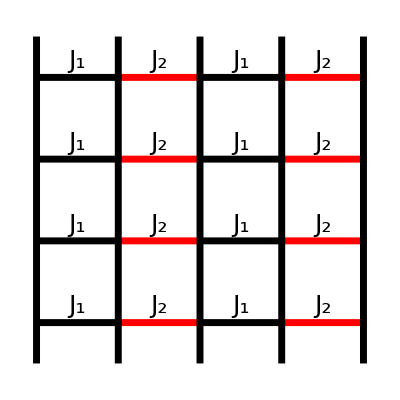

```mathematica
textsize =25;
ratio =1/2000;
thick =Thickness[textsize ratio];
Graphics[{Table[{{thick,Line[{{x,y},{x+1,y}}]},{thick,Red,Line[{{x+1,y},{x+2,y}}]}},{x,0,2,2},{y,0,3,1}],Table[{thick,Line[{{x,-0.5},{x,3.5}}]},{x,0,4}],Table[{Text[Style["J_1",textsize],{x+0.5,y+0.2}],Text[Style["J_2",textsize],{x+1.5,y+0.2}]},{x,0,2,2},{y,0,3}]}]
```

## 2

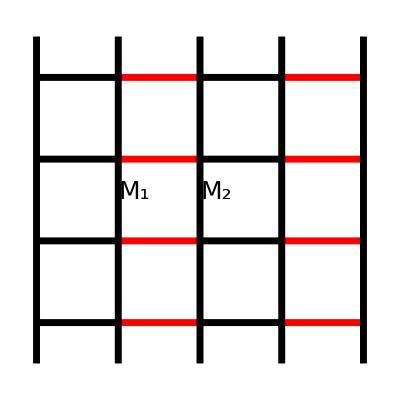

```mathematica
textsize =25;
ratio =1/2000;
thick =Thickness[textsize ratio];
Graphics[{Table[{{thick,Line[{{x,y},{x+1,y}}]},{thick,Red,Line[{{x+1,y},{x+2,y}}]}},{x,0,2,2},{y,0,3,1}],Table[{thick,Line[{{x,-0.5},{x,3.5}}]},{x,0,4}],{EdgeForm[Directive[thick,Darker[Yellow,0.08]]],Opacity[0],Rectangle[{0.6,0.6},{1.4,1.4}]},{EdgeForm[Directive[thick,Darker[Green,0.08]]],Opacity[0],Rectangle[{1.6,0.6},{2.4,1.4}]},Text[Style["M_1",textsize],{1.2,1.6}],Text[Style["M_2",textsize],{2.2,1.6}]}]
```

## 3

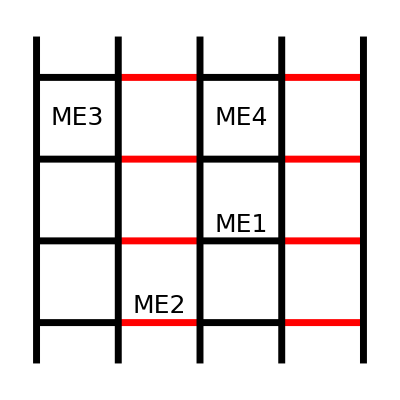

```mathematica
textsize =25;
ratio =1/2000;
thick =Thickness[textsize ratio];
Graphics[{Table[{{thick,Line[{{x,y},{x+1,y}}]},{thick,Red,Line[{{x+1,y},{x+2,y}}]}},{x,0,2,2},{y,0,3,1}],Table[{thick,Line[{{x,-0.5},{x,3.5}}]},{x,0,4}],{EdgeForm[Directive[thick,Darker[Blue,0.08]]],Opacity[0],Rectangle[{0.6,-0.4},{2.4,0.4}]},{EdgeForm[Directive[thick,Darker[Red,0.08]]],Opacity[0],Rectangle[{1.6,0.6},{3.4,1.4}]},
{EdgeForm[Directive[thick,Darker[Green,0.08]]],Opacity[0],Rectangle[{0.6,1.6},{1.4,3.4}]},
{EdgeForm[Directive[thick,Darker[Yellow,0.08]]],Opacity[0],Rectangle[{1.6,1.6},{2.4,3.4}]},Text[Style["ME2",textsize],{1.5,0.2}],Text[Style["ME1",textsize],{2.5,1.2}],Text[Style["ME3",textsize],{0.5,2.5}],Text[Style["ME4",textsize],{2.5,2.5}]}]
```

## 6

```mathematica
SqT[name_,center_,bond_,color_]:=Graphics[{{EdgeForm[Directive[thick,Darker[color,0.08]]],
White,Rectangle[{center[[1]]-0.25,center[[2]]-0.25},{center[[1]]+0.25,center[[2]]+0.25}]},If[bond[[1]]==1,{thick,Line[{{center[[1]]-0.25,center[[2]]},{center[[1]]-0.5,center[[2]]}}]}],
If[bond[[2]]==1,{thick,Line[{{center[[1]],center[[2]]-0.25},{center[[1]],center[[2]]-0.5}}]}],
If[bond[[3]]==1,{thick,Line[{{center[[1]]+0.25,center[[2]]},{center[[1]]+0.5,center[[2]]}}]}],
If[bond[[4]]==1,{thick,Line[{{center[[1]],center[[2]]+0.25},{center[[1]],center[[2]]+0.5}}]}],
Text[Style[name,textsize],center]},ImageSize->Medium]
```

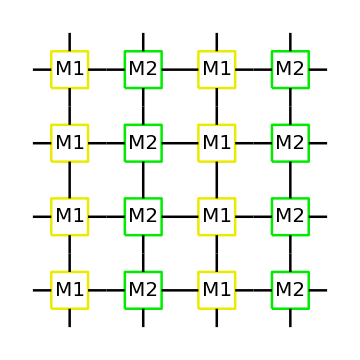

```mathematica
textsize =20;
ratio =1/4000;
thick =Thickness[textsize ratio];
Show[Table[{SqT[M1,{x,y},{1,1,1,1},Yellow],SqT[M2,{x+1,y},{1,1,1,1},Green]},{x,0,2,2},{y,0,3}]]
```

## 4

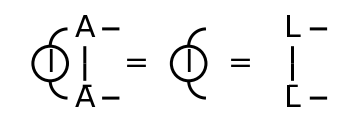

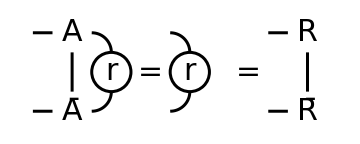

```mathematica
textsize =30;
thick =Thickness[textsize ratio];
Show[SqT[A,{0,0},{0,1,1,0}],SqT[Ā,{0,-1},{0,0,1,1}],CiTL[l,{-0.5,-0.5},{1,1}],
equal[{0.75,-0.5}],CiTL[l,{1.5,-0.5},{1,1}],
equal[{2.25,-0.5}],SqT[L,{3,-0},{0,1,1,0}],SqT[L̄,{3,-1},{0,0,1,1}]]
Show[SqT[A,{0,0},{1,1,0,0}],SqT[Ā,{0,-1},{1,0,0,1}],CiTR[r,{0.5,-0.5},{1,1}],
equal[{1,-0.5}],CiTR[r,{1.5,-0.5},{1,1}],
equal[{2.25,-0.5}],SqT[R,{3,-0},{1,1,0,0}],SqT[R̄,{3,-1},{1,0,0,1}]]
```

## 5

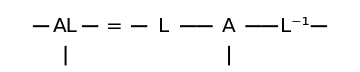

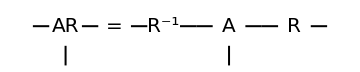

```mathematica
textsize =20;
thick =Thickness[textsize ratio];
Show[SqT[AL,{0,0},{1,1,1,0}],
equal[{0.75,0}],SqT[L,{1.5,0},{1,0,1,0}],SqT[A,{2.5,0},{1,1,1,0}],SqT["L^-1",{3.5,0},{1,0,1,0}]]
Show[SqT[AR,{0,0},{1,1,1,0}],
equal[{0.75,0}],SqT["R^-1",{1.5,0},{1,0,1,0}],SqT[A,{2.5,0},{1,1,1,0}],SqT[R,{3.5,0},{1,0,1,0}]]
```

```mathematica
{EdgeForm[Directive[thick,Darker[Green,0.08]]],Opacity[0],Rectangle[{0.6,1.6},{1.4,3.4}]}
```

## 8

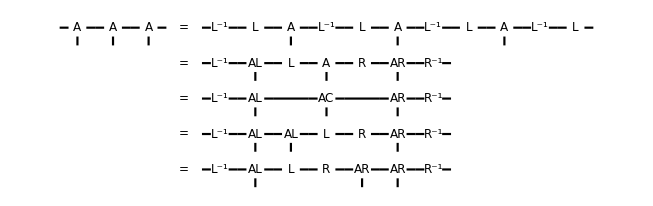

```mathematica
textsize =12;
thick =Thickness[textsize ratio];
Show[SqT[A,{0,0},{1,1,1,0}],SqT[A,{1,0},{1,1,1,0}],SqT[A,{2,0},{1,1,1,0}],
equal[{3,0}],SqT["L^-1",{4,0},{1,0,1,0}],SqT[L,{5,0},{1,0,1,0}],SqT[A,{6,0},{1,1,1,0}],SqT["L^-1",{7,0},{1,0,1,0}],SqT[L,{8,0},{1,0,1,0}],SqT[A,{9,0},{1,1,1,0}],SqT["L^-1",{10,0},{1,0,1,0}],SqT[L,{11,0},{1,0,1,0}],SqT[A,{12,0},{1,1,1,0}],SqT["L^-1",{13,0},{1,0,1,0}],SqT[L,{14,0},{1,0,1,0}],
equal[{3,-1}],SqT["L^-1",{4,-1},{1,0,1,0}],SqT[AL,{5,-1},{1,1,1,0}],SqT[L,{6,-1},{1,0,1,0}],SqT[A,{7,-1},{1,1,1,0}],SqT[R,{8,-1},{1,0,1,0}],SqT[AR,{9,-1},{1,1,1,0}],SqT["R^-1",{10,-1},{1,0,1,0}],
equal[{3,-2}],SqT["L^-1",{4,-2},{1,0,1,0}],SqT[AL,{5,-2},{1,1,1,0}],Graphics[{thick ,Line[{{5.5,-2},{6.5,-2}}],Line[{{7.5,-2},{8.5,-2}}]}],SqT[AC,{7,-2},{1,1,1,0}],SqT[AR,{9,-2},{1,1,1,0}],SqT["R^-1",{10,-2},{1,0,1,0}],
equal[{3,-3}],SqT["L^-1",{4,-3},{1,0,1,0}],SqT[AL,{5,-3},{1,1,1,0}],SqT[AL,{6,-3},{1,1,1,0}],SqT[L,{7,-3},{1,0,1,0}],SqT[R,{8,-3},{1,0,1,0}],SqT[AR,{9,-3},{1,1,1,0}],SqT["R^-1",{10,-3},{1,0,1,0}],
equal[{3,-4}],SqT["L^-1",{4,-4},{1,0,1,0}],SqT[AL,{5,-4},{1,1,1,0}],SqT[L,{6,-4},{1,0,1,0}],SqT[R,{7,-4},{1,0,1,0}],SqT[AR,{8,-4},{1,1,1,0}],SqT[AR,{9,-4},{1,1,1,0}],SqT["R^-1",{10,-4},{1,0,1,0}],Graphics[{EdgeForm[Directive[Dashed,Thickness[0.005],Darker[Red,0.08]]],Opacity[0],Rectangle[{5.5,-0.5},{8.5,-4.5}]}]]
```

## 19

```mathematica
textsize =12;
thick =Thickness[textsize ratio];
Show[SqT[A,{0,0},{1,1,1,0}],SqT[A,{1,0},{1,1,1,0}],SqT[A,{2,0},{1,1,1,0}],
equal[{3,0}],SqT["L^-1",{4,0},{1,0,1,0}],SqT[L,{5,0},{1,0,1,0}],SqT[A,{6,0},{1,1,1,0}],SqT["L^-1",{7,0},{1,0,1,0}],SqT[L,{8,0},{1,0,1,0}],SqT[A,{9,0},{1,1,1,0}],SqT["L^-1",{10,0},{1,0,1,0}],SqT[L,{11,0},{1,0,1,0}],SqT[A,{12,0},{1,1,1,0}],SqT["L^-1",{13,0},{1,0,1,0}],SqT[L,{14,0},{1,0,1,0}],
equal[{3,-1}],SqT["L^-1",{4,-1},{1,0,1,0}],SqT[AL,{5,-1},{1,1,1,0}],SqT[L,{6,-1},{1,0,1,0}],SqT[A,{7,-1},{1,1,1,0}],SqT[R,{8,-1},{1,0,1,0}],SqT[AR,{9,-1},{1,1,1,0}],SqT["R^-1",{10,-1},{1,0,1,0}],
equal[{3,-2}],SqT["L^-1",{4,-2},{1,0,1,0}],SqT[AL,{5,-2},{1,1,1,0}],Graphics[{thick ,Line[{{5.5,-2},{6.5,-2}}],Line[{{7.5,-2},{8.5,-2}}]}],SqT[AC,{7,-2},{1,1,1,0}],SqT[AR,{9,-2},{1,1,1,0}],SqT["R^-1",{10,-2},{1,0,1,0}],
equal[{3,-3}],SqT["L^-1",{4,-3},{1,0,1,0}],SqT[AL,{5,-3},{1,1,1,0}],SqT[AL,{6,-3},{1,1,1,0}],SqT[L,{7,-3},{1,0,1,0}],SqT[R,{8,-3},{1,0,1,0}],SqT[AR,{9,-3},{1,1,1,0}],SqT["R^-1",{10,-3},{1,0,1,0}],
equal[{3,-4}],SqT["L^-1",{4,-4},{1,0,1,0}],SqT[AL,{5,-4},{1,1,1,0}],SqT[L,{6,-4},{1,0,1,0}],SqT[R,{7,-4},{1,0,1,0}],SqT[AR,{8,-4},{1,1,1,0}],SqT[AR,{9,-4},{1,1,1,0}],SqT["R^-1",{10,-4},{1,0,1,0}],Graphics[{EdgeForm[Directive[Dashed,Thickness[0.005],Darker[Red,0.08]]],Opacity[0],Rectangle[{5.5,-0.5},{8.5,-4.5}]}]]
```

-Graphics-

## 9

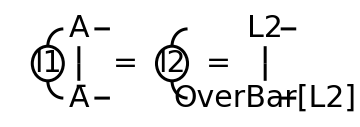

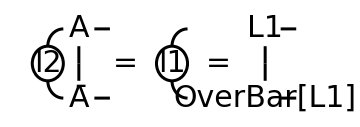

```mathematica
textsize =30;
thick =Thickness[textsize ratio];
Show[SqT[A,{0,0},{0,1,1,0}],SqT[Ā,{0,-1},{0,0,1,1}],CiTL[l1,{-0.5,-0.5},{1,1}],
equal[{0.75,-0.5}],CiTL[l2,{1.5,-0.5},{1,1}],
equal[{2.25,-0.5}],SqT[L2,{3,-0},{0,1,1,0}],SqT[OverBar[L2],{3,-1},{0,0,1,1}]]
Show[SqT[A,{0,0},{0,1,1,0}],SqT[Ā,{0,-1},{0,0,1,1}],CiTL[l2,{-0.5,-0.5},{1,1}],
equal[{0.75,-0.5}],CiTL[l1,{1.5,-0.5},{1,1}],
equal[{2.25,-0.5}],SqT[L1,{3,-0},{0,1,1,0}],SqT[OverBar[L1],{3,-1},{0,0,1,1}]]
```

## 10

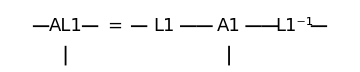

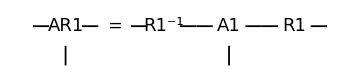

```mathematica
textsize =18;
thick =Thickness[textsize ratio];
Show[SqT[AL1,{0,0},{1,1,1,0}],
equal[{0.75,0}],SqT[L1,{1.5,0},{1,0,1,0}],SqT[A1,{2.5,0},{1,1,1,0}],SqT["L1^-1",{3.5,0},{1,0,1,0}]]
Show[SqT[AR1,{0,0},{1,1,1,0}],
equal[{0.75,0}],SqT["R1^-1",{1.5,0},{1,0,1,0}],SqT[A1,{2.5,0},{1,1,1,0}],SqT[R1,{3.5,0},{1,0,1,0}]]
```

## 11

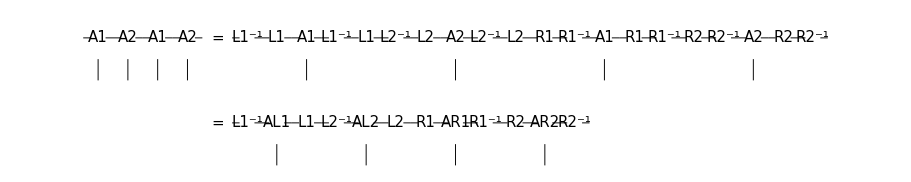

```mathematica
textsize =15;
ratio=1/20000;
thick =Thickness[textsize ratio];
Show[SqT[A1,{0,0},{1,1,1,0}],SqT[A2,{1,0},{1,1,1,0}],SqT[A1,{2,0},{1,1,1,0}],SqT[A2,{3,0},{1,1,1,0}],
equal[{4,0}],SqT["L1^-1",{5,0},{1,0,1,0}],SqT[L1,{6,0},{1,0,1,0}],SqT[A1,{7,0},{1,1,1,0}],SqT["L1^-1",{8,0},{1,0,1,0}],SqT[L1,{9,0},{1,0,1,0}],SqT["L2^-1",{10,0},{1,0,1,0}],SqT[L2,{11,0},{1,0,1,0}],SqT[A2,{12,0},{1,1,1,0}],SqT["L2^-1",{13,0},{1,0,1,0}],SqT[L2,{14,0},{1,0,1,0}],SqT["R1",{15,0},{1,0,1,0}],SqT["R1^-1",{16,0},{1,0,1,0}],SqT[A1,{17,0},{1,1,1,0}],SqT["R1",{18,0},{1,0,1,0}],SqT["R1^-1",{19,0},{1,0,1,0}],SqT["R2",{20,0},{1,0,1,0}],SqT["R2^-1",{21,0},{1,0,1,0}],SqT[A2,{22,0},{1,1,1,0}],SqT["R2",{23,0},{1,0,1,0}],SqT["R2^-1",{24,0},{1,0,1,0}],
equal[{4,-1}],SqT["L1^-1",{5,-1},{1,0,1,0}],SqT[AL1,{6,-1},{1,1,1,0}],SqT["L1",{7,-1},{1,0,1,0}],SqT["L2^-1",{8,-1},{1,0,1,0}],SqT[AL2,{9,-1},{1,1,1,0}],SqT["L2",{10,-1},{1,0,1,0}],SqT["R1",{11,-1},{1,0,1,0}],SqT[AR1,{12,-1},{1,1,1,0}],SqT["R1^-1",{13,-1},{1,0,1,0}],SqT["R2",{14,-1},{1,0,1,0}],SqT[AR2,{15,-1},{1,1,1,0}],SqT["R2^-1",{16,-1},{1,0,1,0}]]
```